# Fat Skinny Potential

## Potential

Pot: 1. + x^2*(-3.375 + x*(1.6875 + x*(2.84765625 + (-2.84765625 + 0.7119140625*x)*x)))

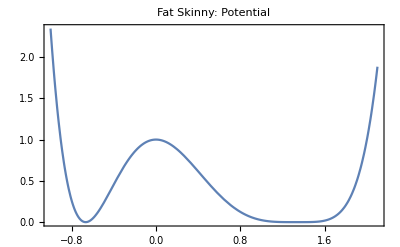

```mathematica
Pot=(3x-4)^4*(3x+2)^2/1024.;


Print["Pot: ",InputForm[HornerForm[Pot]]]

Plot[Pot,{x,-1,2.1},PlotRange->All,Frame->True,PlotLabel->"Fat Skinny: Potential"]
```

## Force

Force: 0. + x*(6.75 + x*(-5.0625 + x*(-11.390625 + (14.23828125 - 4.271484375*x)*x)))

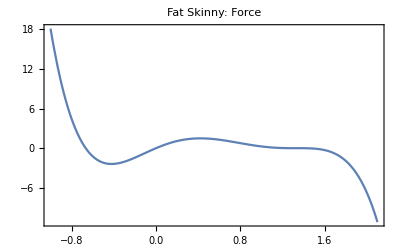

```mathematica
Force=-D[Pot,x];

Print["Force: ",InputForm[HornerForm[Force]]]

Plot[Force,{x,-1,2.1},PlotRange->All,Frame->True,PlotLabel->"Fat Skinny: Force"]
```

## Hessian

Hessian: -6.75 + x*(10.125 + x*(34.171875 + x*(-56.953125 + 21.357421875*x)))

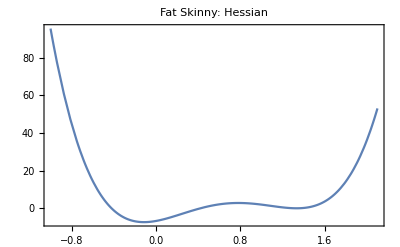

```mathematica
Hess=D[Pot,{x,2}];

Print["Hessian: ",InputForm[HornerForm[Hess]]]

Plot[Hess,{x,-1,2.1},PlotRange->All,Frame->True,PlotLabel->"Fat Skinny: Hessian"]
```